NIntegrate::inumr: The integrand (ⅇ^(-√(100+k^2) Abs[x]) k BesselJ[0,100 k])/(√(100+k^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.02404825557695773}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

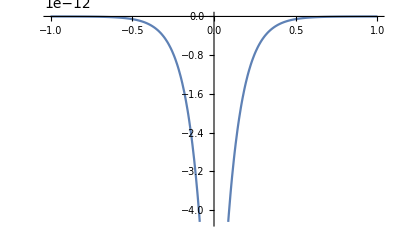

```mathematica
V[x_,a_,d_]:=NIntegrate[BesselJ[0,k * d]*k/(k^2+a^2)^(1/2)*Exp[-(k^2+a^2)^(1/2)*Abs[x]],{k,0,Infinity}];
Plot[V[x,10,100],{x,-1,1}]
```